```mathematica
ClearAll["Global`*"]
```

```mathematica
SetOptions[EvaluationNotebook[],Background->LightGray]
```

```mathematica
SetDirectory["/Users/spencerbryngelson/Desktop/Fortran/EV_spectral/D"];
```

```mathematica
data=Import[#,"Table"]&/@FileNames["eval*"];
```

```mathematica
Table[vec[j]=data[[j]],{j,1,Length[data]}];
```

```mathematica
Do[ReEv[i]=Table[vec[i][[j,1]],{j,1,Length[vec[i]]}],{i,1,Length[data]}]
```

```mathematica
Do[SortReEv1[i]=Drop[Sort[ReEv[i]],-1],{i,1,Length[data]}]
```

```mathematica
Do[SortReEv2[i]=Drop[Sort[ReEv[i]],-2],{i,1,Length[data]}]
```

```mathematica
Do[MaxEv[i]=Max[ReEv[i]],{i,1,Length[data]}]
```

```mathematica
Do[MaxEv1[i]=Max[SortReEv1[i]],{i,1,Length[data]}]
```

```mathematica
Do[MaxEv2[i]=Max[SortReEv2[i]],{i,1,Length[data]}]
```

```mathematica
xs=Table[i*0.02,{i,1,Length[data]}];
ys=Table[MaxEv[i],{i,1,Length[data]}];
ys1=Table[MaxEv1[i],{i,1,Length[data]}];
ys2=Table[MaxEv2[i],{i,1,Length[data]}];
pairs=Thread[{xs,ys}];
pairs1=Thread[{xs,ys1}];
pairs2=Thread[{xs,ys2}];
```

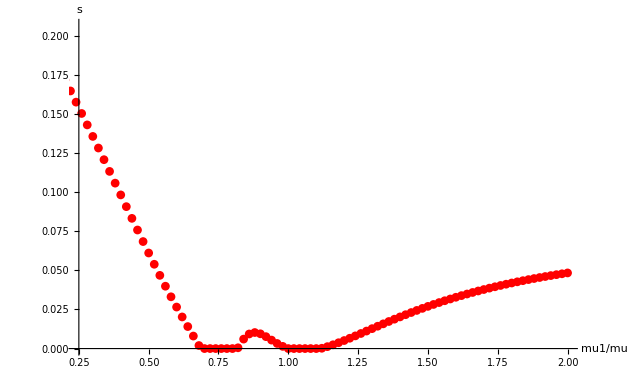

```mathematica
l1=ListPlot[pairs,Joined->False,PlotRange->{{0.25,2},Automatic},PlotStyle->{PointSize[0.01],Red},AxesLabel->{"mu1/mu2","s"},LabelStyle->Directive[14]]
```

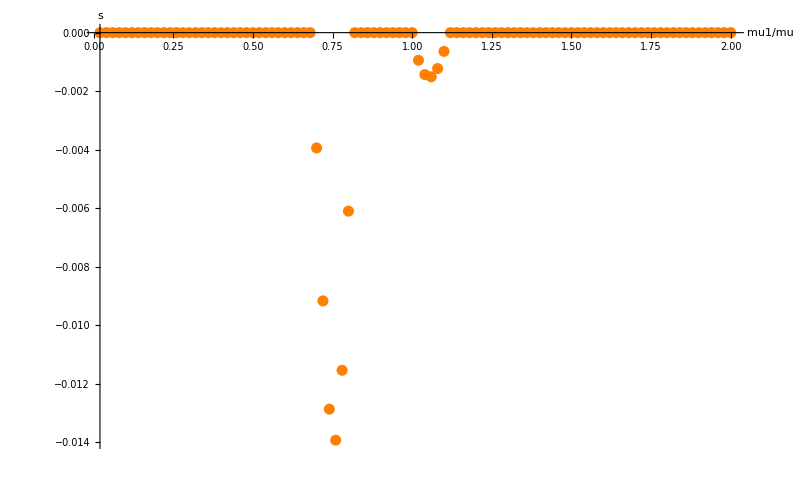

```mathematica
l3=ListPlot[pairs1,Joined->False,PlotRange->All,PlotStyle->{PointSize[0.01],Orange},AxesLabel->{"mu1/mu2","s"},LabelStyle->Directive[14]]
```

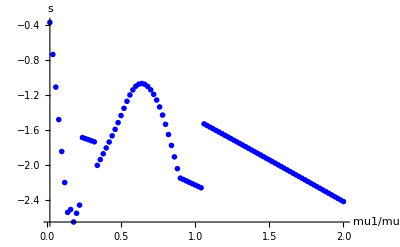

```mathematica
l2=ListPlot[pairs2,Joined->False,PlotRange->All,PlotStyle->{PointSize[0.01],Blue},AxesLabel->{"mu1/mu2","s"},LabelStyle->Directive[14]]
```

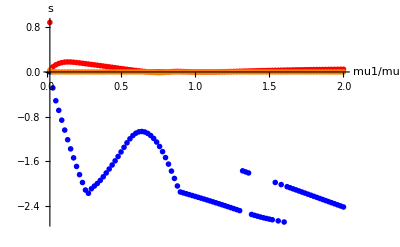

```mathematica
Show[l1,l2,l3,PlotRange->All]
```

```mathematica
SetDirectory["/Users/spencerbryngelson/Desktop/Fortran/EV_Spectral/V"]
```

/Users/spencerbryngelson/Desktop/Fortran/EV_spectral/V

```mathematica
ClearAll["Global`*"]
```

```mathematica
data=Import[#,"Table"]&/@FileNames["x.*"];
```

```mathematica
Table[vec[j]=data[[j]],{j,1,Length[data]}];
Table[realvec[i]=Table[vec[i][[j,1]],{j,1,Length[data]}],{i,1,Length[data]}];
Table[imvec[i]=Table[vec[i][[j,2]],{j,1,Length[data]}],{i,1,Length[data]}];
```

```mathematica
Dimensions[data]
```

{180,180,2}

```mathematica
Length[data]
```

180

```mathematica
(* only first two have true nonzero eigenvalues *)
```

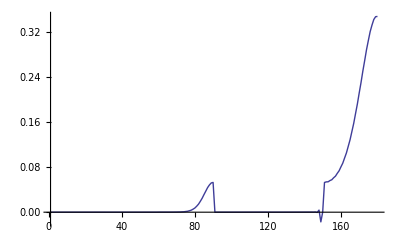
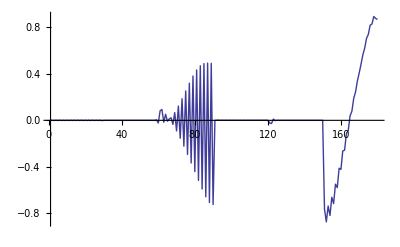
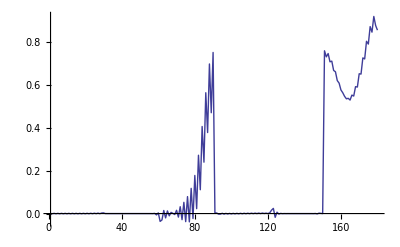
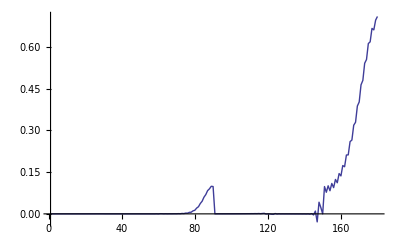
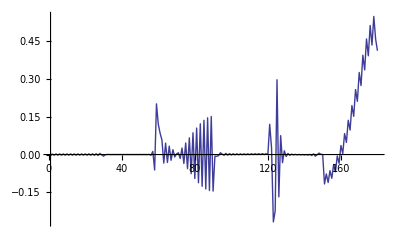
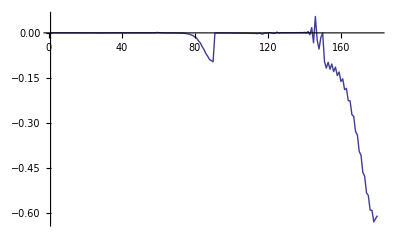
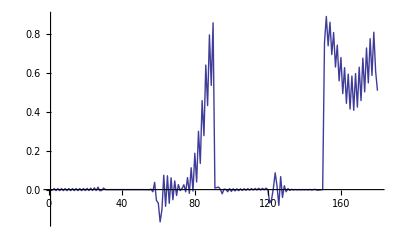
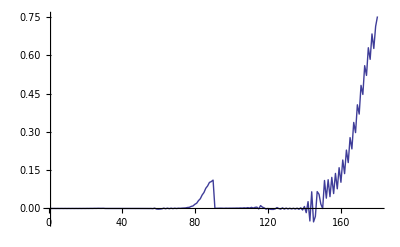
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListPlot[realvec[j],PlotRange->All,Joined->True],{j,1,Length[data]}]
```

```mathematica
ListPlot[realvec[10],PlotRange->All,Joined->True]
```

-Graphics-